## Hayes & Adams (2017) Mathematica Notebook 2

## About this notebook

This document is a PDF created from a Wolfram Mathematica notebook file prepared by Mark A. Hayes during December, 2016, following the general approach for age structured population analysis discussed in Hayes (2011). This code and output analyzes the stable stochastic population model used in the Hayes and Adams 2017 PLOS ONE manuscript. This notebook is used to demonstrate that the stochastic population model results in an average ending population of about 2,000 females. The vital rates used in this notebook match the vital rates used in Notebook 1, which was used for sensitivity and elasticity analysis of the model. In the matrix model below, the first row of the matrix model can be confusing. This row shows (1) the probability of a bat surviving the year and then (2) giving birth to a female pup, and is thus survival for the age class times the birth rate for the age class. If you would like a copy of the original Mathematica notebook, please contact MAH at hayesm@usgs.gov or hayes.a.mark@gmail.com.  

Mark A. Hayes
January 2, 2017

```mathematica
SetDirectory[NotebookDirectory[]]
```

\\IGSKBACBFS2\groups\bts\t\mah\manuscripts\2016\Hayes & Adams 2016 - Bat pop modeling - PLOS ONE\revision - fall winter 2016\Plos One - Data package

### Defining the model:

```mathematica
SAave = 0.79;
SAmin = SAave*0.90;
SAmax = SAave*1.10;

SFave= SAave*0.64;
SFmin = SFave*0.90;
SFmax = SFave*1.10;

adultBirthRate=0.425;

aReproAve=SAave*adultBirthRate;
aReproMin = aReproAve*0.90;
aReproMax = aReproAve*1.10;

jReproAve=0.90*adultBirthRate*SFave;
jReproMin = jReproAve*0.90;
jReproMax = jReproAve*1.10;

m={{jReproAve,aReproAve,aReproAve,aReproAve},{SFave,0,0,0},{0,SAave,0,0},{0,0,SAave,SAave}};

runs = 10000;
j = 0;

MatrixForm[m]
Eigenvalues[m,1]
```

(0.193392 | 0.33575 | 0.33575 | 0.33575
0.5056 | 0 | 0 | 0
0 | 0.79 | 0 | 0
0 | 0 | 0.79 | 0.79)

{1.00036}

### Setting up the Monte Carlo simulation:

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax}]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax}]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax}]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax}]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin,jReproMax}]]))+
(Nne*(RandomReal[TriangularDistribution[{aReproMin,aReproMax}]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin,aReproMax}]]))+
(Nthree*(RandomReal[TriangularDistribution[{aReproMin,aReproMax}]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

### Calculating statistics and visualizing output:

2063.92

414.594

756.

4201.

(0.193392 | 0.33575 | 0.33575 | 0.33575
0.5056 | 0 | 0 | 0
0 | 0.79 | 0 | 0
0 | 0 | 0.79 | 0.79)

{1.00036}

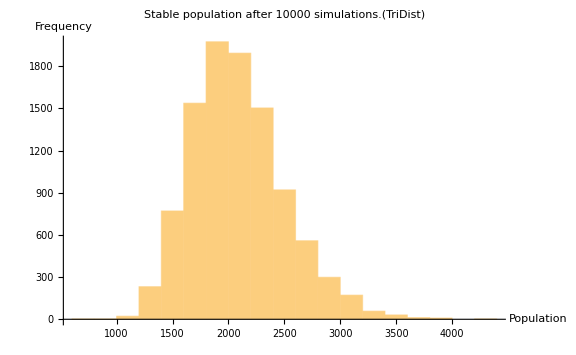

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]

MatrixForm[m]
Lambda=Eigenvalues[m,1]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,
PlotLabel->StringJoin["Stable population after ", ToString[runs],
" simulations.", "(TriDist)"], AxesLabel->{"Population", "Frequency"}]
```